# Free precession case

## m<1 case

```mathematica
free1[ϵ_,δ_,θ0_,P_,t_]:=Module[{L1,L2,L3},
I1=1;
ω0=2π/P;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
L1=Sin[θ0]*JacobiCN[ωp*t,m];
L2=Sin[θ0]*(1+δ)^0.5*JacobiSN[ωp*t,m];
L3=Cos[θ0]*JacobiDN[ωp*t,m];
{L1,L2,L3}

]
period1[ϵ_,δ_,θ0_,P_]:=Module[{T},
I1=1;
ω0=2π/P;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=4*I3/(ϵ L Cos[θ0])(1+δ)^0.5 EllipticK[m];
{T}

]
```

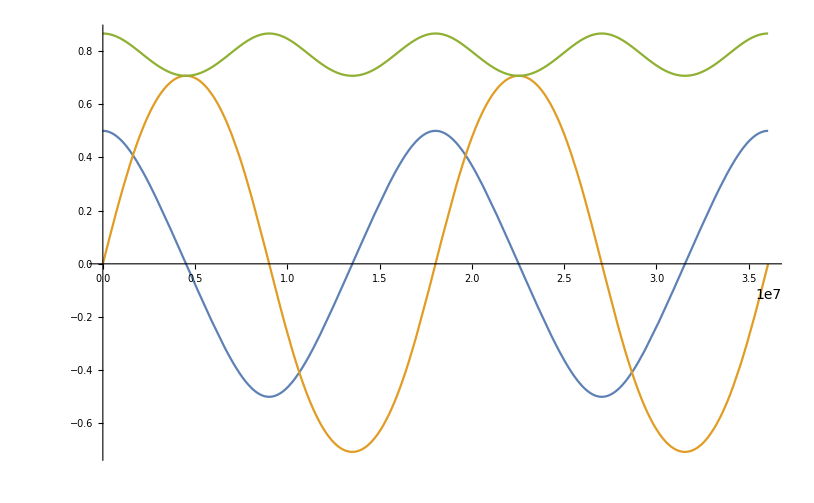

```mathematica
ϵ=10^-7;δ=1;θ0=30/180*π;P=1;

Plot[{free1[ϵ,δ,θ0,P,t][[1]],free1[ϵ,δ,θ0,P,t][[2]],free1[ϵ,δ,θ0,P,t][[3]]},{t,0,2*period1[ϵ,δ,θ0,P][[1]]},Background->White]
```

### test with numerical solution

```mathematica
free2[ϵ_,δ_,θ_,P_]:=Module[{sol},
ω0=2π/P;τp=1/ω0/ϵ;
ϵ1=ϵ*δ/(1+ϵ+δ);
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t],u2'[t]==(ϵ*ω0*u1[t]*u3[t])/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t])/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]
```

{{u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…]}}

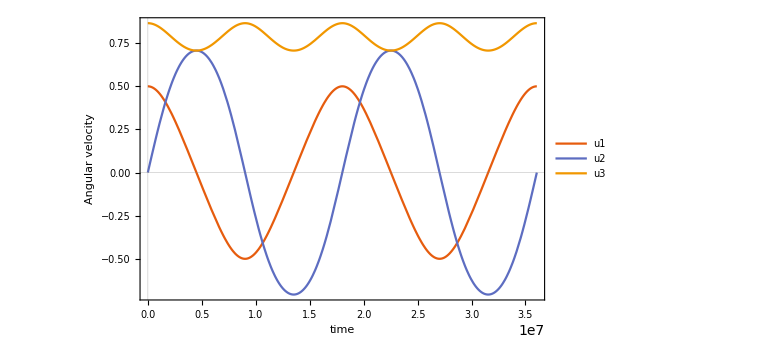

```mathematica
sol=Evaluate[free2[ϵ,δ,θ0,P]]
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,2*period1[ϵ,δ,θ0,P][[1]]},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```

## m>1 case (transform by redefinition of the moment of inertia tensor)

```mathematica
free3[ϵ_,δ_,θ0_,P_,t_]:=Module[{L1,L2,L3},
I1=1;
ω0=2π/P;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
ωp1=Sqrt[m]*ωp;
δ1=1/δ;
m1=1/m;
L1=Sin[π/2-θ0]*JacobiCN[ωp1*t,m1];
L2=Sin[π/2-θ0]*(1+δ1)^0.5*JacobiSN[ωp1*t,m1];
L3=Cos[π/2-θ0]*JacobiDN[ωp1*t,m1];
{L1,L2,L3}

]
period2[ϵ_,δ_,θ0_,P_]:=Module[{T},
I1=1.0;
ω0=2π/P;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
ωp1=Sqrt[m]*ωp;
δ1=1/δ;
m1=1/m;
T=-4*I3/(ϵ L Sin[θ0])(1+δ1)^0.5 EllipticK[m1];
{T}

]
```

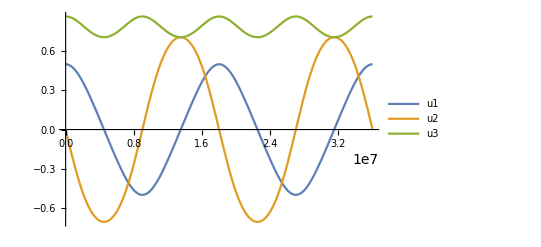

```mathematica
ϵ=-10^-7;δ=1;θ0=60/180*π;P=1;
Plot[{free3[ϵ,δ,θ0,P,t][[1]],free3[ϵ,δ,θ0,P,t][[2]],free3[ϵ,δ,θ0,P,t][[3]]},{t,0,2*period2[ϵ,δ,θ0,P][[1]]},Background->White,PlotLegends->{"u1","u2","u3"}]
```

{{u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…]}}

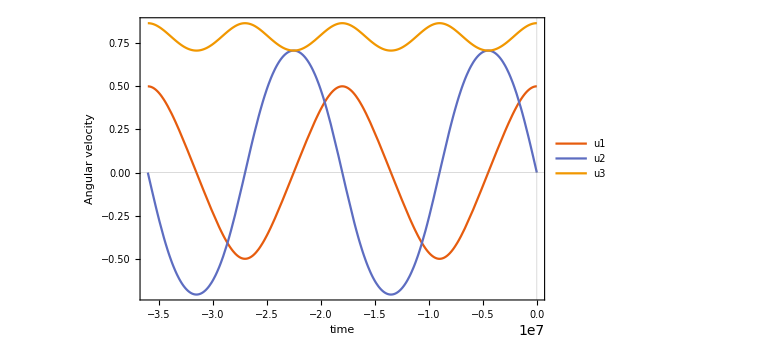

```mathematica
ϵ=-10^-7;δ=1;θ0=30/180*π;P=1;
sol=Evaluate[free2[ϵ,δ,θ0,P]]
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,2*period1[ϵ,δ,θ0,P][[1]]},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```